```mathematica
n=11;
```

```mathematica
(*k=AdjacencyMatrix[RandomGraph[{n,15}]];
AdjacencyGraph[k]*)
```

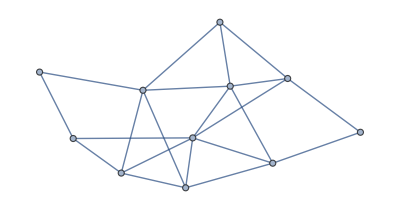
```mathematica
k1=-Graphics-;
```

```mathematica
k=AdjacencyMatrix[k1]
```

SparseArray[<42>, {11, 11}]

```mathematica
data={0.6562722556236429,-0.34657670139825003,0.23728565072404703,-0.5347469428961505,1.8997829817652392,1.4296796397474802,-1.735727298690614,-1.7816500083767144,2.277924371534762,1.3312030304500866,-0.06828965655804965};
```

```mathematica
m=3;
(*data=RandomVariate[VonMisesDistribution[0,0],n];*)
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns=Table[{Subscript[∅,i]'[t]==6-1/n Sum[k[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅,j][t]-Subscript[∅,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅,i][0]==data[[i]]},{i,1,n}];
vars=Table[Subscript[∅,i][t],{i,1,n}];
sol=NDSolve[eqns,vars,{t,0,10000}];
Do[Subscript[z,i][t_]:=Evaluate[Subscript[∅,i][t]/.sol],{i,1,n}];
Do[Subscript[zz,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅,i][t]/.sol)],{i,1,n}];
data1[t_]:=Flatten[Table[Subscript[zz,i][t],{i,1,n}]];
tt=10000;
lista=Sort[Table[Mod[Subscript[z,i][tt],2Pi][[1]],{i,1,n}]];
lisboj[t_]:=Table[Mod[Subscript[z,i][t],2Pi][[1]],{i,1,n}];
SomeGraph=AdjacencyGraph[k];
Table[lista[[i]]-lista[[i+1]],{i,1,n-1}]
ukupfrust[t_]:=Sum[k[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z,j][t]-Subscript[z,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}]
ukupfrust[5000]
data2=Flatten[Table[Mod[Subscript[z,i][tt],2Pi],{i,1,n}]]
```

{0.,-1.5708,0.,-1.5708,0.,0.,-1.5708,0.,0.,-7.27596×10^-12}

{0.}

{2.59782,1.02703,2.59782,5.73942,5.73942,4.16862,5.73942,5.73942,4.16862,4.16862,1.02703}

```mathematica
zvuk={2,1,2,4,4,3,4,4,3,3,1};
```

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];
Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];
findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

```mathematica
a=Table[findAllRoots[Sin[(Subscript[z,i][t])/2],{t,0,20}],{i,1,n}];
```

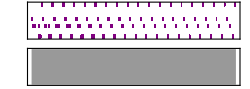

```mathematica
Sound[Flatten[Table[Table[If[Round[a[[i]][[j]],0.02]==t,If[zvuk[[i]]==1,SoundNote["G",{t,t+0.1},"Piano"],If[zvuk[[i]]==2,SoundNote["B",{t,t+0.1},"Piano"],If[zvuk[[i]]==3,SoundNote["D",{t,t+0.1},"Piano"],SoundNote["F",{t,t+0.1},"Piano"]]]],SoundNote[None,{t,t+0.1}]],{i,1,n},{j,1,Length[a[[i]]]}],{t,0,20,0.02}]],{0,66.733}]
```

```mathematica
Export["sim4_piano.mp3",%29]
```

sim4_piano.mp3

```mathematica
Export["sim4.mid", %29]
```

sim4.mid

```mathematica
granica=20;
```

```mathematica
video[t_]:=Grid[{{GraphPlot[SomeGraph,PlotStyle->{Gray,Thickness[0.008]},VertexRenderingFunction->Function[{pos,vid},{(*color for the disk*)Hue@Rescale[lisboj[t][[Sequence@@vid]],{0,2 Pi}],(*the disk itself*)Disk[pos,0.17],(*vertex number centered on the disk*)Text[Style[vid,20,Black,Bold],pos]}],ImageSize->700],Show[{Module[{pts},pts=ReIm@data1[t];
ListPlot[pts,PlotStyle->{Black,Opacity[0],PointSize[0.025]},Epilog->MapIndexed[Text[Style[#2[[1]],16,Black,Bold],#1+{0.045,0.045}   (*small offset*)]&,pts]]],With[{sectors=360},angle=2 Pi/sectors;
Graphics[{Table[{Hue[i/sectors],EdgeForm[{Thick,Hue[i/sectors]}],Disk[{0,0},1,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]],Module[{pts},pts=ReIm@data1[t];
ListPlot[pts,PlotStyle->{Black,PointSize[0.025]},Epilog->MapIndexed[Text[Style[#2[[1]],14,Black,Bold],#1+{0.03,0.03}   (*small offset*)]&,pts]]],ListPlot[{0,1},PlotStyle->Directive[Gray,PointSize[.025]]]},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,25],Axes->True,AxesOrigin->{0,0},PlotRange->{{-1.1,1.1},{-1.1,1.1}},ImagePadding->40,AspectRatio->1],Show[{Plot[ukupfrust[tt],{tt,0,t+0.0000000001},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},PlotStyle->Directive[If[Chop[ukupfrust[10000]][[1]]==0,Red,Blue],Thickness[0.01]]]},AxesOrigin->{0,0},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},ImageSize->600,Frame->True,FrameStyle->Directive[Black,25]]}},Spacings->0]
```

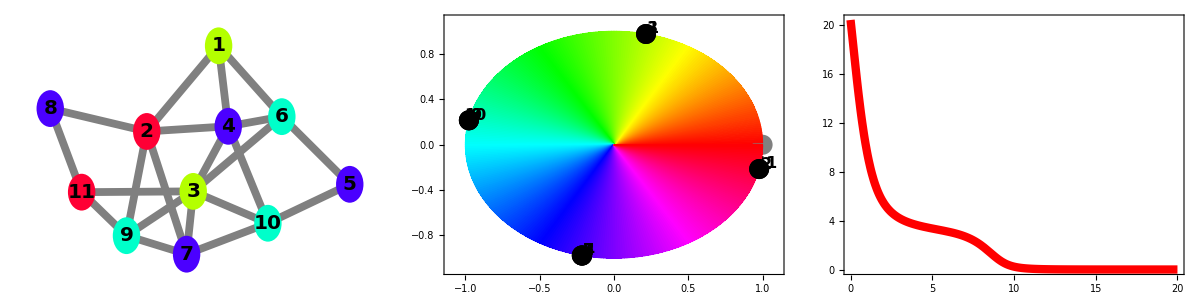

```mathematica
video[20]
```

```mathematica
simulaci1=Table[video[t],{t,0,20,0.02}];
```

```mathematica
Export["SM4.AVI",simulaci1]
```